```mathematica
<<MASStoolbox`
<<XML`
SetDirectory[NotebookDirectory[]];
SetDirectory[".."];
<<util`
```

# SB2 Systems Biology: Simulation of Dynamic Network States

## Salvage pathway

### Construct model

#### Build model

```mathematica
chemicalFormulas={r5p^c->"H9C5O8P",ade^c->"H5C5N5",ado^c->"H13C10N5O4",imp^c->"H12C10N4O8P",ino^c->"H12C10N4O5",hyp^c->"H4C5N4O",r1p^c->"H9C5O8P",prpp^c->"H8C5O14P3",amp^c->"H13C10N5O7P",adp^c->"H13C10N5O10P2",atp^c->"H13C10N5O13P3",phos^c->"HO4P",h^c->"H",h2o^c->"H2O",nh3^c->"H3N"};
rxns={Overscript[ado^c+h2o^c⇌ino^c+nh3^c, vada],(ade^c⇌∅)^vade,(ado^c⇌∅)^vado,Overscript[ade^c+h2o^c+prpp^c⇌amp^c+2 phos^c, vadprt],Overscript[ado^c+atp^c⇌adp^c+amp^c, vak],Overscript[amp^c+h2o^c⇌ado^c+h^c+phos^c, vampase],Overscript[amp^c+h2o^c⇌imp^c+nh3^c, vampda],(hyp^c⇌∅)^vhyp,Overscript[h2o^c+imp^c⇌h^c+ino^c+phos^c, vimpase],(ino^c⇌∅)^vino,(nh3^c⇌∅)^vnh3,(phos^c⇌∅)^vphos,Overscript[ino^c+phos^c⇌hyp^c+r1p^c, vpnpase],Overscript[r1p^c⇌r5p^c, vprm],Overscript[2 atp^c+r5p^c⇌2 adp^c+h^c+prpp^c, vprppsyn],(amp^c⇌∅)^vamp,(h^c⇌∅)^vh,(h2o^c⇌∅)^vh2o,Overscript[adp^c+h^c+phos^c⇌atp^c+h2o^c, vatpgen]};
eqConstants={Underscript[K, vak]->1000000,Underscript[K, vampase]->1000000 Millimole Liter^-1,Underscript[K, vada]->1000000 Millimole Liter^-1,Underscript[K, vampda]->1000000 Millimole Liter^-1,Underscript[K, vimpase]->1000000 Millimole Liter^-1,Underscript[K, vpnpase]->0.09,Underscript[K, vprm]->13.3,Underscript[K, vprppsyn]->1000000,Underscript[K, vadprt]->1000000 Millimole Liter^-1,Underscript[K, vade]->1,Underscript[K, vado]->1,Underscript[K, vino]->1,Underscript[K, vhyp]->1,Underscript[K, vphos]->1,Underscript[K, vnh3]->1,Underscript[K, vatpgen]->1000000 Liter Millimole^-1,Underscript[K, vh]->1,Underscript[K, vh2o]->1,Underscript[K, vamp]->1};
ststConc={r5p^c->0.00494 Millimole Liter^-1,ade^c->0.001 Millimole Liter^-1,ado^c->0.0012 Millimole Liter^-1,imp^c->0.01 Millimole Liter^-1,ino^c->0.001 Millimole Liter^-1,hyp^c->0.002 Millimole Liter^-1,r1p^c->0.06 Millimole Liter^-1,prpp^c->0.005 Millimole Liter^-1,amp^c->0.08672812499999999 Millimole Liter^-1,adp^c->0.29 Millimole Liter^-1,atp^c->1.6 Millimole Liter^-1,phos^c->2.5 Millimole Liter^-1,h^c->0.00006309573444801929 Millimole Liter^-1,h2o^c->0.99999976 Millimole Liter^-1,nh3^c->0.091 Millimole Liter^-1};
ststFluxes={"vak"->0.12 Millimole Hour^-1 Liter^-1,"vampase"->0.12 Millimole Hour^-1 Liter^-1,"vampda"->0.014 Millimole Hour^-1 Liter^-1,"vimpase"->0.014 Millimole Hour^-1 Liter^-1,"vada"->0.01 Millimole Hour^-1 Liter^-1,"vpnpase"->0.014 Millimole Hour^-1 Liter^-1,"vprm"->0.014 Millimole Hour^-1 Liter^-1,"vatpgen"->0.148 Millimole Hour^-1 Liter^-1,"vprppsyn"->0.014 Millimole Hour^-1 Liter^-1,"vadprt"->0.014 Millimole Hour^-1 Liter^-1,"vado"->-0.009999999999999995 Millimole Hour^-1 Liter^-1,"vade"->-0.014 Millimole Hour^-1 Liter^-1,"vino"->0.01 Millimole Hour^-1 Liter^-1,"vhyp"->0.014 Millimole Hour^-1 Liter^-1,"vamp"->0. Millimole Hour^-1 Liter^-1,"vh"->0. Millimole Hour^-1 Liter^-1,"vh2o"->-0.024000000000000007 Millimole Hour^-1 Liter^-1,"vphos"->0. Millimole Hour^-1 Liter^-1,"vnh3"->0.024 Millimole Hour^-1 Liter^-1};
xtrnConc={ado^Xt->0.0012001 Millimole Liter^-1,ade^Xt->0.00100014 Millimole Liter^-1,ino^Xt->0.0009999 Millimole Liter^-1,hyp^Xt->0.00199986 Millimole Liter^-1,phos^Xt->2.5 Millimole Liter^-1,nh3^Xt->0.0909999 Millimole Liter^-1,amp^Xt->0.09540093749999999 Millimole Liter^-1,h^Xt->0.00006309573444801929 Millimole Liter^-1,metabolite[_,"Xt"]->Millimole Liter^-1};
salvage=constructModel[rxns,
UnitChecking->True,
ElementalComposition->chemicalFormulas,
Parameters->Join[eqConstants,xtrnConc],
InitialConditions->Join[ststConc,ststFluxes],
Ignore->{m["h","c"],m["h2o","c"]}
];
salvagePercTuned=updateRules[calcPERC[salvage,"AtEquilibriumDefault"->100000],{Subscript[k, vh]^⟶->100000,Subscript[k, vade]^⟶->100000,Subscript[k, vino]^⟶->100000,Subscript[k, vhyp]^⟶->100000,Subscript[k, vnh3]^⟶->100000,Subscript[k, vphos]^⟶->100000,Subscript[k, vamp]^⟶->100000}];
updateParameters[salvage,salvagePercTuned];
updateNotes[salvage,defaultInitializationNotes[]];
SetDirectory[NotebookDirectory[]];
Export["../../models/SB2/salvage.m.gz",salvage]
```

calcPERC::atequilibrium: Reaction "vphos" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 100000 (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::atequilibrium: Reaction "vamp" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 100000 (this value can be specified using the option "AtEquilibriumDefault").

calcPERC::atequilibrium: Reaction "vh" is either at equlibrium or not active. Forward rate constant k_StyleBox[ is set to 100000 (this value can be specified using the option "AtEquilibriumDefault").

General::stop: Further output of calcPERC :: atequilibrium will be suppressed during this calculation.

adjustUnits::noUnitsProvidedRateConst: No units provided for k_StyleBox[. (InterpretationBox[)^(1 - rxnOrder)(InterpretationBox[)^(rxnOrder - 1)(InterpretationBox[)^-1 assumed.

General::stop: Further output of adjustUnits :: noUnitsProvidedRateConst will be suppressed during this calculation.

../../models/SB2/salvage.m.gz

```mathematica
SortBy[stripUnits@salvagePercTuned,Last]
```

{k_vampda^⟶→0.161424,k_vatpgen^⟶→0.204138,k_vprm^⟶→0.234787,k_vprppsyn^⟶→1.10703,k_vampase^⟶→1.38363,k_vimpase^⟶→1.4,k_vada^⟶→8.33333,k_vpnpase^⟶→12.,k_vak^⟶→62.5008,k_vadprt^⟶→3140.46,k_vado^⟶→100000.,k_vade^⟶→100000,k_vamp^⟶→100000,k_vh^⟶→100000,k_vhyp^⟶→100000,k_vino^⟶→100000,k_vnh3^⟶→100000,k_vphos^⟶→100000,k_vh2o^⟶→100000.}

```mathematica
{concSol,fluxSol}=simulate[salvage,{t,0,10000}];
```

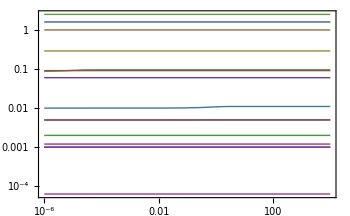

```mathematica
plotSimulation[concSol]
```

```mathematica
TableForm[List@@@FilterRules[salvage["Parameters"],_rateconst]]
```

k_vada^⟶ | 8.33333 Hour^-1
k_vado^⟶ | 100000. Hour^-1
k_vadprt^⟶ | 3140.46 Liter Hour^-1 Millimole^-1
k_vak^⟶ | 62.5008 Liter Hour^-1 Millimole^-1
k_vampase^⟶ | 1.38363 Hour^-1
k_vampda^⟶ | 0.161424 Hour^-1
k_vimpase^⟶ | 1.4 Hour^-1
k_vpnpase^⟶ | 12. Liter Hour^-1 Millimole^-1
k_vprm^⟶ | 0.234787 Hour^-1
k_vprppsyn^⟶ | 1.10703 Liter^2 Hour^-1 Millimole^-2
k_vh2o^⟶ | 100000. Hour^-1
k_vatpgen^⟶ | 0.204138 Liter Hour^-1 Millimole^-1
k_vh^⟶ | 100000 Hour^-1
k_vade^⟶ | 100000 Hour^-1
k_vino^⟶ | 100000 Hour^-1
k_vhyp^⟶ | 100000 Hour^-1
k_vnh3^⟶ | 100000 Hour^-1
k_vphos^⟶ | 100000 Hour^-1
k_vamp^⟶ | 100000 Hour^-1

```mathematica
({{, "G", "K", "G/K", "k"}, {"vak", 0, 1.*^6, 0, 62.50081873325923}, {"vampase", 0, 1.*^6, 0, 1.3836345337814195}, {"vampda", 0, 1.*^6, 0, 0.16142403063477634}, {"vimpase", 0, 1.*^6, 0, 1.4000003580835985}, {"vada", 0, 1.*^6, 0, 8.33333609166758}, {"vpnpase", 0.048, 0.09, 0.533, 12.}, {"vprm", 0.082, 13.3, 0.006, 0.2347867752755151}, {"vatpgen", 0, 1.*^6, 0, 3352.633032780616}, {"vprppsyn", 0, 1.*^6, 0, 1.107034412957788}, {"vadprt", 0, 1.*^6, 0, 3140.4583322004664}, {"vado", 1., 1., 1., 100000}, {"vade", 1., 1., 1., 100000}, {"vino", 1., 1., 1., 100000}, {"vhyp", 1., 1., 1., 100000}, {"vamp", 1., 1., 1., 100000}, {"vh", 1., 1., 1., 100000}, {"vh2o", 1., 1., 1., 100000}, {"vphos", 1., 1., 1., 100000}, {"vnh3", 1., 1., 1., 100000}});
```

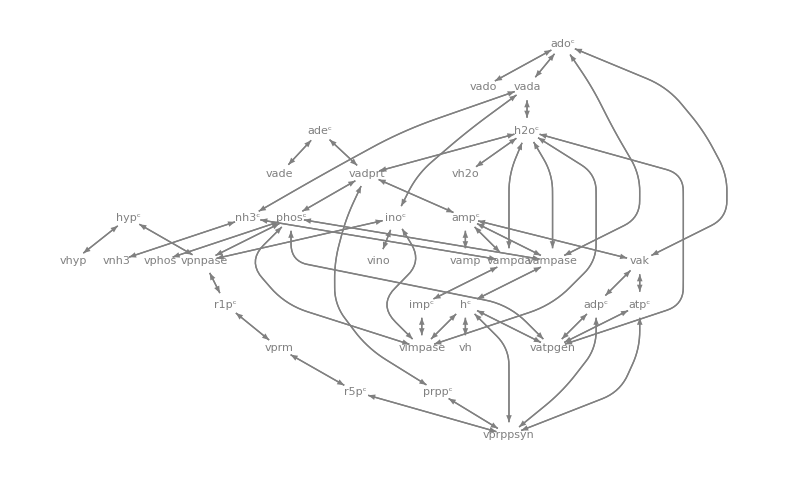

```mathematica
visualizePathways[reactions2bipartite[salvage["Reactions"]],
DirectedEdges->True,PlotStyle->{GrayLevel[0.5],Arrowheads[.012]},
"MetaboliteRenderingFunction"->({Style[Text[StandardForm@#2,#1],
Background->Opacity[.6,White]]}&),"ReactionRenderingFunction"->({Style[Text[StandardForm@#2,#1],Larger,Background->Opacity[.6,LightGray]]}&),ImageSize->800,MultiedgeStyle->None]
```